```mathematica
Needs["HypothesisTesting`"]
```

Toolbar, Buttons and Misc. Functions

```mathematica
gameSettings=<| "roulType"-> "usRoul", "bankRoll"->10000, "minBet"->5, "maxBet"->1000, "initialBet"->5|>;
simulationSettings=<|"gamesPerTrial"-> 100, "numOfTrials"->100|>;
plotLiveUpdt = False;distEst=False;
```

```mathematica
{globRoulType, globBankRoll, globMinBet, globMaxBet, globInitBet} =Values[gameSettings];
{globGamesPerTrial, globNumOfTrials}=Values[simulationSettings];

barContents:=Module[{localRoulType, localBankRoll,localMinBet,localMaxBet,localInitBet,localGamesPerTrial, localNumOfTrials},
Column[{Row[{
"Roulette Type : ", PopupMenu[Dynamic[globRoulType],{"usRoul", "enRoul"}],
" Bank Roll: ",InputField[Dynamic[globBankRoll],FieldSize->4],
" Min Bet: ",InputField[Dynamic[globMinBet],FieldSize->4],
" Max.Bet: ",InputField[Dynamic[globMaxBet],FieldSize->4],
" Initial Bet: ",InputField[Dynamic[globInitBet],FieldSize->3]
}],
Row[{
"Games per Trial: ", InputField[Dynamic[globGamesPerTrial],FieldSize->5],
" Num of Trials: ", InputField[Dynamic[globNumOfTrials],FieldSize->5],"    ",
Checkbox[Dynamic[plotLiveUpdt]],"Live Plot (slow)  ",
Checkbox[Dynamic[distEst]],"Dist. estimate ",
Button["Update",(gameSettings=AssociationThread[Keys[gameSettings]-> {globRoulType, globBankRoll, globMinBet, globMaxBet, globInitBet}]; simulationSettings=AssociationThread[Keys[simulationSettings]-> {globGamesPerTrial, globNumOfTrials}];)]
}]
}]
]
```

```mathematica
SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[ToBoxes[barContents]],
"DockedCell",Background->Lighter[Gray, 0.75]]];
```

```mathematica
deletePrints[] :=Module[{},
NotebookFind[SelectedNotebook[], "Print", All, CellStyle];NotebookDelete[]]
deleteTempPrints[] :=Module[{},
NotebookFind[SelectedNotebook[],"PrintTemporary", All, CellStyle];NotebookDelete[]]
```

```mathematica
runBtnImg:=Image[Graphics[{Darker@Green,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Run",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
runBtn:=Button[runBtnImg,runSim[],Appearance->None, Method->"Queued"];
stopBtnImg:=Image[Graphics[{Red,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Stop",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
stopBtn:=Button[stopBtnImg,(endSim=1),Appearance->None];
clearImg:=Image[Graphics[{Gray,Disk[{0,0},0.6],Inset[Disk[{0,0},1]],
Inset[Style["Clear",{White, Bold,30}]]},ImageSize->Tiny,Background->None]];
clearBtn:=Button[clearImg,deletePrints[],Appearance->None];
```

```mathematica
{euRoul=Import["http://www.onlinecasinoreporter.com/wp-content/uploads/2012/07/european-roulette-table.gif"],
usRoul=Import["http://www.roulette-games.com/images/american_roulette_layout.gif"]};
```

Simulate roulette spin. Returns amount to multiply original bet by or -1 if the best is lost
TODO: parse number in string to number
TODO: Handle errors of incorrect inputs

```mathematica
simSpin[roulType_,betName_]:=Module[{denom=Switch[roulType,"enRoul",37,"usRoul",38,_,Abort[]],winOrLose,mult,oneToOneDist,twoToOneDist,straightUp},
oneToOneDist=BinomialDistribution[1,18/denom];(* Bet on Red, Black, Even, Odd*)
twoToOneDist=BinomialDistribution[1,12/denom];(* Bet on a column *) 
straightUp=BinomialDistribution[1,1/denom];(* Bet on single number *)

If[StringQ[betName],(* A few possibilities of bets...*)
If[StringMatchQ[betName,{"1to18","even","red","black","odd","19to36"},IgnoreCase->True], winOrLose=RandomVariate[oneToOneDist];mult=1;];
If[StringMatchQ[betName,{"1st12","2nd12","3rd12","2to1"},IgnoreCase->True], winOrLose=RandomVariate[twoToOneDist];mult=2;];
,(* Else, bet is single numbers 0 to 36*)
winOrLose=RandomVariate[straightUp]; mult=35;];
If[winOrLose==1,mult,-1]
]
```

Runs one trial with specified global parameters in: gameSettings and simulationSettings
- Choose betting type and strategy here

```mathematica
runTrial[]:=Module[{bankHistory={gameSettings["bankRoll"]},betAmount=gameSettings["minBet"],betType="black"},

Do[
(* simulate roulette spin with given bet and append result to bankHistory*)
bankHistory=Append[bankHistory, Last[bankHistory]+betAmount*simSpin[gameSettings["roulType"], betType]];


(* BETTING STRATEGY HERE .... changes bet amount of betType*)
If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=1]; (* constant bet size*)
(*If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=2];*) (* double after every loss*)


(* Game boundries:
 - Can't have negative bankroll- break instead
- Can't bet more than we have (bet all we have instead)
- Must stay within max/min betting limits       *)
If[(Last[bankHistory]≤ 0 ), Break[]];
If[betAmount> Last[bankHistory],betAmount=Last[bankHistory]];
betAmount=betAmount/.{x_/;x<gameSettings["minBet"]->gameSettings["minBet"],x_/;x>gameSettings["maxBet"]->gameSettings["maxBet"]};

,simulationSettings["gamesPerTrial"]-1];

bankHistory
]
```

Expected Value formula for multiple events:
E(X) 	= ∑X * P(X)
 E_blackOrRed = (18/38)(5) + (20/38)(-5) = -0.263158

Runs simulation with specified parameters and calculate metrics
TODO: Try decreasing Dynamic update rate for less frequent rendering
TODO: Look into interpolation for faster rendering
TODO: Look into Parallelize for faster rendering

#### runSim[]

```mathematica
runSim[]:=Module[{},
trialHistory={};
finalBankRoll={};
gameHistory={};
trialNum=0;
endSim= 0;

If[plotLiveUpdt,
dynPlot=Dynamic[Style[ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"],Antialiasing->False]];
];

PrintTemporary["Running simulation... ", Dynamic[trialNum], " of ", simulationSettings["numOfTrials"]];
PrintTemporary[ProgressIndicator[Dynamic[trialNum],{0,simulationSettings["numOfTrials"]}]];
If[plotLiveUpdt,PrintTemporary[dynPlot];];

Table[
If[endSim==1,Abort[],
singleGameHistory=runTrial[];
finalBankRoll=Append[finalBankRoll, Last[singleGameHistory]];(* snarf relevant data from trial for later analysis *)
trialHistory=Append[trialHistory, singleGameHistory];
trialNum++; 
];
,simulationSettings["numOfTrials"]
];
deleteTempPrints[];

PrintTemporary["Calculating distribution..."];
(*------ Calculate some stats -------*) 
If[distEst,guessDist=Quiet[FindDistribution[finalBankRoll]];];
meanBankRoll=N[Mean[finalBankRoll]];
stdev=N[StandardDeviation[finalBankRoll]];
varian=N[Variance[finalBankRoll]];
(*resultCI = MeanCI[finalBankRoll-gameSettings["bankRoll"], ConfidenceLevel->.95]/simulationSettings["gamesPerTrial"];*)
(*expVal=Round[Mean[finalBankRoll-gameSettings["bankRoll"]]/simulationSettings["gamesPerTrial"],0.0001];*)
expVal=(Expectation[x,x\[Distributed]guessDist]-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"];
stdevExpVal=N[StandardDeviation[(finalBankRoll-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]]];
If[plotLiveUpdt,
finalPlot = dynPlot/.Dynamic->Evaluate;,
finalPlot= ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"];
];



Print[Style["Summary:",Bold,16]];
Print[Row[{
finalPlot,
Column[{
Grid[{
{"Games per trial: ", simulationSettings["gamesPerTrial"]},
{"Number of trials: ", simulationSettings["numOfTrials"]},
(*{"% of bankrupcies: ", N[Count[finalBankRoll,0]/simulationSettings["numOfTrials"]]*100},*)
{"Average earnings: ",  N[Mean[finalBankRoll]-gameSettings["bankRoll"]]},
{"Average final bankroll: ",meanBankRoll},
{"Expected value : ",ToString[expVal](*<>" ± "<>ToString[Round[( Differences[resultCI][[1]]/2),0.0001]]*)}
(*{"95% CI of E(x) +-: ", (1.96*stdevExpVal)}*)
},Frame->All,Background->{{LightGray}}],

Show[Histogram[finalBankRoll,100,"PDF",
Epilog->{Directive[{Blue,Thin,Dashed}],
Line[{{meanBankRoll,0},{meanBankRoll,600}}],
Line[{{(meanBankRoll-2.571*stdev),0},{(meanBankRoll-2.571*stdev),1}}],
Line[{{(meanBankRoll+2.571*stdev),0},{(meanBankRoll+2.571*stdev),1}}]
}],
Plot[PDF[NormalDistribution[meanBankRoll,stdev],x],{x,meanBankRoll-3stdev,meanBankRoll+3stdev}],ImageSize->Medium,PlotLabel-> "Final Bankroll",PlotRange->{{meanBankRoll-5stdev,meanBankRoll+5stdev},All}]
}]
}]];

]
```

```mathematica
{runBtn,stopBtn,clearBtn}
```

{-Graphics-,-Graphics-,-Graphics-}

## Making code cloud-deployable

#### runSimFunc[inputs_]

```mathematica
runSimFunc[roulType_, bankRoll_, minBet_,maxBet_, initBet_, gamePerTrial_, trials_]:=Module[{trialHistory={}, finalBankRoll={}, gameHistory={}, trialNum=0,dynPlot,plotLiveUpdt=False},

(* Updates values from function into global settings *)
(gameSettings=AssociationThread[Keys[gameSettings]-> {roulType, bankRoll, minBet, maxBet, initBet}]; simulationSettings=AssociationThread[Keys[simulationSettings]-> {gamePerTrial, trials}];);

(* Run trials without Prints *)
Table[
singleGameHistory=runTrial[];

(* snarf relevant data from trial for later analysis *)
finalBankRoll=Append[finalBankRoll, Last[singleGameHistory]];
trialHistory=Append[trialHistory, singleGameHistory];
,simulationSettings["numOfTrials"]
];

(*-------- Calculate some stats *) 
meanBankRoll=N[Mean[finalBankRoll]];
stdev=N[StandardDeviation[finalBankRoll]];
varian=N[Variance[finalBankRoll]];
(*resultCI = MeanCI[finalBankRoll-gameSettings["bankRoll"], ConfidenceLevel->.95]/simulationSettings["gamesPerTrial"];*)
expVal=Round[Mean[finalBankRoll-gameSettings["bankRoll"]]/simulationSettings["gamesPerTrial"],0.0001];
stdevExpVal=N[StandardDeviation[(finalBankRoll-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]]];

finalPlot= ListLinePlot[trialHistory,
GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large,MaxPlotPoints->100,PerformanceGoal->"Speed"];

guessDist=FindDistribution[finalBankRoll];

Row[{finalPlot,
Column[{
Grid[{
{"Games per trial: ", simulationSettings["gamesPerTrial"]},
{"Number of trials: ", simulationSettings["numOfTrials"]},
(*{"% of bankrupcies: ", N[Count[finalBankRoll,0]/simulationSettings["numOfTrials"]]*100},*)
{"Average earnings: ",  N[Mean[finalBankRoll]-gameSettings["bankRoll"]]},
{"Average final bankroll: ", N[Mean[finalBankRoll]]}
(*{"Expected value : ",ToString[expVal]<>" ± "<>ToString[Round[( Differences[resultCI][[1]]/2),0.0001]]},*)
(*{"resultCI: ", ToString[resultCI]}*)
(*{"95% CI of E(x) +-: ", (1.96*stdevExpVal)}*)

},Frame->All,Background->{{LightGray}}]
,
Show[Histogram[finalBankRoll,100,"PDF"],
Plot[PDF[NormalDistribution[meanBankRoll,stdev],x],{x,meanBankRoll-3stdev,meanBankRoll+3stdev}],ImageSize->Medium,PlotLabel-> "Final Bankroll",PlotRange-> All]
}]

}]
]
```

### FormFunction for CloudDeploy[]

```mathematica
myCloudForm=FormFunction[{
"RouletteType"-> {"usRoul", "enRoul"}, "Bankroll"-> <|"Interpreter"->"Number","Input"->10000|>, "MinBet"->  <|"Interpreter"->"Number","Input"->5|>, "MaxBet"->  <|"Interpreter"->"Number","Input"->1000|>, "InitialBet" ->  <|"Interpreter"->"Number","Input"->5|>,
"GamesPerTrial"->  <|"Interpreter"->"Number","Input"->100|>,
"TrialsPerSimulation"->  <|"Interpreter"->"Number","Input"->100|>}, 

runSimFunc[#RouletteType, #Bankroll, #MinBet, #MaxBet, #InitialBet, #GamesPerTrial, #TrialsPerSimulation]&, 

FormLayoutFunction->Function[Column[{
Row[{#["RouletteType"]," ", #["Bankroll"] }],
Row[{#["MinBet"]," ",#["MaxBet"]," ",#["InitialBet"]}],
Row[{#["GamesPerTrial"]," ",#["TrialsPerSimulation"]}] 
}]
],
AppearanceRules-><|"Title"->"Game Info: " , "SubmitLabel"-> "Simulate"|>]
```

FormFunction[]

```mathematica
CloudDeploy[myCloudForm]
```

CloudObject[https://www.wolframcloud.com/objects/bb1d05f3-a979-4058-9c84-2e9144be85c9]

#### --- Testing package functionality in cloud deploy

```mathematica
CloudDeploy[MeanCI[{-155,-65,-55,-65,-35,-25,-5,-25,55,15,15,-35,-95,-115,-45,-75,-55,-75,5,-65,5,-5,35,-85,-45,25,5,-55,25,-15,-95,65,15,-15,-15,-25,-65,-65,5,45,-115,65,-105,25,-45,-45,-55,25,25,-35,-15,-5,-5,-35,-15,35,45,-95,-5,5,15,15,-45,65,-5,-15,-85,-85,-125,-15,65,-75,-5,-35,-75,5,85,-35,-95,-5,45,15,-135,-25,-45,65,-5,15,-15,-75,65,-85,-35,-5,-75,-25,55,-15,25,-65},ConfidenceLevel->0.95]]
```

CloudObject[https://www.wolframcloud.com/objects/09f44780-958c-4b1a-93fe-114dd2d9accc]

### Delete cloud objects...

```mathematica
cloudObjs=CloudObjects[".Objects"]
```

{}

```mathematica
DeleteObject/@cloudObjs
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Calculating own Confidence interval (to remove Needs[“HypothesisTesting`”] )

## Sample data

```mathematica
dataSet=RandomVariate[NormalDistribution[5,2],50]
{N@Mean[dataSet],MeanCI[dataSet,ConfidenceLevel->0.95]}
```

{6.58726,5.1936,3.12285,3.42664,6.90524,3.72284,3.68878,-0.338943,5.58315,7.35887,5.96144,4.9435,2.95126,6.08718,6.48742,4.35745,5.15047,5.93799,5.32601,1.41888,6.21963,-0.765925,5.30016,4.82462,8.08347,5.20302,3.12205,8.59089,3.48809,5.49288,2.35449,5.69489,4.40007,4.30429,6.1446,3.80285,7.31601,6.65506,5.19394,3.93474,4.04833,5.44044,6.66077,7.56278,8.1816,5.86467,8.26835,9.06044,7.01284,4.28782}

{5.1924,{4.60745,5.77734}}

```mathematica
meanSE=StandardDeviation[dataSet]/Sqrt[Length[dataSet]];
tScore=1.96;(* 95% of data *)
{ Mean[dataSet]-tScore*meanSE,Mean[dataSet]+tScore*meanSE }
```

{4.62188,5.76291}

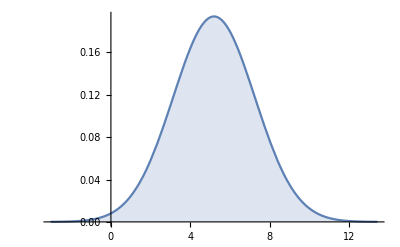

```mathematica
tmpMean=Mean[dataSet];
tmpStdev=StandardDeviation[dataSet];
distPlot=Plot[PDF[NormalDistribution[tmpMean,tmpStdev],x],{x,(tmpMean-4tmpStdev),tmpMean+4tmpStdev},
Filling->Axis]
```

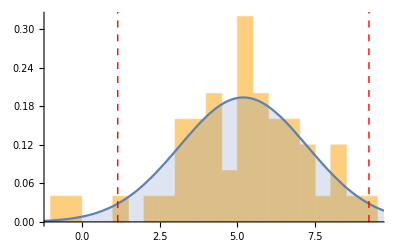

```mathematica
Show[
Histogram[dataSet,20,"PDF"],
distPlot,
Epilog->{Directive[{Red,Thick,Dashed}],
Line[{{tmpMean+1.96tmpStdev,0},{tmpMean+1.96tmpStdev,600}}],
Line[{{tmpMean-1.96tmpStdev,0},{tmpMean-1.96tmpStdev,600}}]
}]
```

```mathematica
Probability[1<x<8, x\[Distributed]NormalDistribution[tmpMean,tmpStdev]]
```

0.927484

## Calculating for actual data

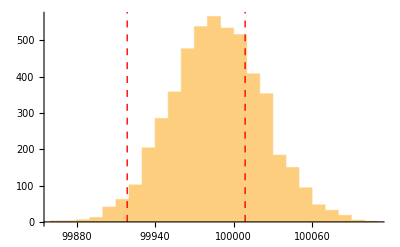

```mathematica
Histogram[finalBankRoll,PlotRange-> All,
Epilog->{Directive[{Red,Thick,Dashed}],
Line[{{mean,0},{mean,600}}],
Line[{{(mean-stdevMult*stdev),0},{(mean-stdevMult*stdev),600}}],
Line[{{(mean+stdevMult*stdev),0},{(mean+stdevMult*stdev),600}}]
}]
```

```mathematica
N@Mean[finalBankRoll]
```

99987.5

```mathematica
tmpDist=FindDistribution[finalBankRoll]
```

PascalDistribution[98586,0.985958]

```mathematica
(Expectation[x,x\[Distributed]tmpDist]-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]
```

-0.242384

```mathematica
FindRoot[Probability[(mean-stdevMult*stdev)<x<(mean+stdevMult*stdev),x\[Distributed]tmpDist]==  0.95,{stdevMult,3},PrecisionGoal->2,AccuracyGoal->2,MaxIterations->5]
```

$Aborted

```mathematica
stdevMult=2.571;
Probability[(mean-stdevMult*stdev)<x<(mean+stdevMult*stdev),x\[Distributed]tmpDist]
```

0.688420397507

```mathematica
(mean-stdevMult*stdev)
```

99830.4

```mathematica
((mean-stdevMult*stdev)-gameSettings["bankRoll"])
```

-169.639

```mathematica
(Expectation[x,x\[Distributed]guessDist]-gameSettings["bankRoll"])/50
```

-0.261589

```mathematica
N@StandardDeviation[finalBankRoll]
```

35.0821

```mathematica
(Expectation[x-35.0821,x\[Distributed]guessDist]-gameSettings["bankRoll"])/50
```

-0.963231

```mathematica
Expectation[x,x\[Distributed]guessDist]
```

99974.3

```mathematica
Integrate[E^x, x\[Distributed]guessDist]
```

ⅇ^x (x\[Distributed]PascalDistribution[97516,0.975411])